```mathematica
(* dx variabile, dt = 0.001, t_steps = 10^8 *)
```

```mathematica
dt linear=
{{0.001,0.0008624834},
{0.002,0.0008568326},
{0.005,0.0008851089},
{0.01,0.000830232},
{0.02,0.0012804259},
{0.05,0.0010448659},
{0.1,0.0018529778},
{0.2,0.0020923729}};
```

```mathematica
dt exp=
{{0.001,0.0031730811},
{0.002,0.0032458904},
{0.005,0.0033167495},
{0.01,0.004259015},
{0.02,0.004086487},
{0.05,0.003450455},
{0.1,0.0050671913},
{0.2,0.006265371}};
```

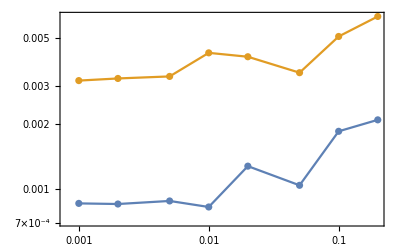

```mathematica
ListLogLogPlot[
{dt linear,dt exp},
Mesh->All,Joined->True,GridLines->Automatic,Frame->True]
```